```mathematica
Manipulate[
Module[{height,δ1,L1,δ2,v1,v2,h1,h2},
height=0.055;δ1=0.02;L1=0.048;(*δ2=0.0235;*)

v1=0.02495;
v2=v1;

h1[v_]=0.1+0.8*(v-0.001247)/(0.02495-0.001247);
h2[v_]=h1[v]+0.075;

Graphics[{
{Opacity[0.7,RGBColor[0.16,1.,0.36]],Rectangle[{0,0},{0.7,h1[v1]}],Rectangle[{1.25,0},{1.95,h1[v2]}]},
{EdgeForm[Thick],GrayLevel[0.4],Rectangle[{0,h1[v1]},{0.7,h2[v1]}],Rectangle[{1.25,h1[v2]},{1.95,h2[v2]}]},
{Thickness[0.005],Line[{{0,1.12},{0,0},{0.7,0},{0.7,1.12}}],Line[{{1.25,1.12},{1.25,0},{1.95,0},{1.95,1.12}}]},

{EdgeForm[{Thick,Black}],RGBColor[0.76,0.04,0.],
If[cs==1,
{Polygon[{{1.25,h2[v2]},{1.25,h2[v2]+0.1},{1.25+0.1,h2[v2]}}],Polygon[{{1.95,h2[v2]},{1.95,h2[v2]+0.1},{1.95-0.1,h2[v2]}}]},
{Polygon[{{1.25,h1[v2]},{1.25,h1[v2]-0.1},{1.25+0.1,h1[v2]}}],Polygon[{{1.95,h1[v2]},{1.95,h1[v2]-0.1},{1.95-0.1,h1[v2]}}]}]
},

{EdgeForm[Thick],RGBColor[0.,0.55,0.64],
Table[{
Rectangle[{n*δ1+(n-1)*L1,h2[v1]},{n*(δ1+L1),h2[v1]+height}],
Rectangle[{1.25+n*δ1+(n-1)*L1,h2[v2]},{1.25+n*(δ1+L1),h2[v2]+height}]},{n,1,10}],
},

(*Text[Style[Row[{Subscript[Style["P",Italic],"ext"]," = ",NumberForm[Pext1,{3,1}]," MPa"}],18],{0.35,0.27+h1[v1]}],
Text[Style[Row[{Subscript[Style["P",Italic],"ext"]," = ",NumberForm[Pext2,{3,1}]," MPa"}],18],{1.6,0.27+h1[v2]}],*)

Text[Framed@Style[Column[{
"constant pressure",
Row[{"W = ",," kJ/mol"}]
}],18],{0.35,1.45}],

Text[Framed@Style["constant volume",18],{1.6,1.45}],

},ImageSize->{475,350},PlotRange->{{-0.15,2.15},{-0.01,1.65}}]
],
Control[{{cs,1,""},{1->" heat gas ",2->" cool gas "},Setter}]
]
```

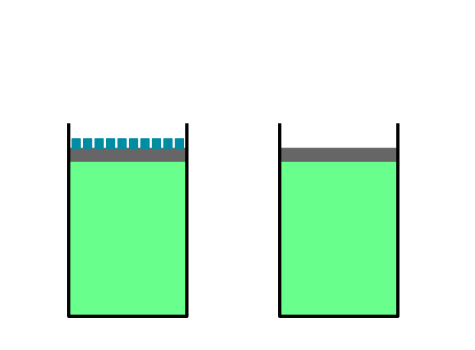

```mathematica
Module[{height,δ1,L1,δ2,wb1,wt1,wb2,wt2},
(*height=0.055;
δ1=0.015;
L1=0.0475;
δ2=0.0235;*)
height=0.055;
δ1=0.02;
L1=0.048;
(*δ2=0.0235;*)

wb1=1;wt1=1;wb2=1;wt2=1;

Graphics[{
{Opacity[0.7,RGBColor[0.16,1.,0.36]],Rectangle[{0,0},{0.7,0.9}],Rectangle[{1.25,0},{1.95,0.9}]},
{EdgeForm[Thick],GrayLevel[0.4],Rectangle[{0,0.9},{0.7,0.975}],Rectangle[{1.25,0.9},{1.95,0.975}]},
{Thickness[0.005],Line[{{0,1.12},{0,0},{0.7,0},{0.7,1.12}}],Line[{{1.25,1.12},{1.25,0},{1.95,0},{1.95,1.12}}]},

{EdgeForm[Thick],RGBColor[0.,0.55,0.64],
Table[Rectangle[{n*δ1+(n-1)*L1,0.975},{n*(δ1+L1),0.975+height}],{n,1,10}],
(*Table[Rectangle[{0.25*(2*δ1+L1)+n*δ2+(n-1)*L1,0.975+height},{0.25*(2*δ1+L1)+n*(δ2+L1),0.975+2*height}],{n,1,9*wt1}],*)
(*Table[Rectangle[{1.25+n*δ1+(n-1)*L1,0.975},{1.25+n*(δ1+L1),0.975+height}],{n,1,11*wb2}],
Table[Rectangle[{1.25+0.25*(2*δ1+L1)+n*δ2+(n-1)*L1,0.975+height},{1.25+0.25*(2*δ1+L1)+n*(δ2+L1),0.975+2*height}],{n,1,9*wt2}]*)},

(*Text[Style[Row[{Subscript[Style["P",Italic],"ext"]," = ",NumberForm[Pext1,{3,1}]," MPa"}],18],{0.35,0.27+0.9}],
Text[Style[Row[{Subscript[Style["P",Italic],"ext"]," = ",NumberForm[Pext2,{3,1}]," MPa"}],18],{1.6,0.27+h1[v2]}],*)
},ImageSize->{475,350},PlotRange->{{-0.15,2.15},{-0.01,1.65}}]
]
```